```mathematica
fX[x_]:=2*x*Exp[-x^2/theta2]/theta2
CondSweep[x_]:=Exp[-x^2/alpha2]

gamma2[c_]:=(c-1)/1
delta[c_]:=c/(c+1)
arci[c_]:=2*ArcCot[Sqrt[1+gamma2[c]]]/Sqrt[1+gamma2[c]]
```

```mathematica
theta2=c0/(rho*mu)
alpha2=(c1-c0)/(rho*mu)
```

c0/(mu rho)

(-c0+c1)/(mu rho)

```mathematica
(c1-c0)/(mu rho)
```

```mathematica
Integrate[CondSweep[x]*fX[x],{x,0,Infinity}]
```

ConditionalExpression[(-c0+c1)/c1, Re[(c1 mu rho)/(c0^2-c0 c1)]<0]

1

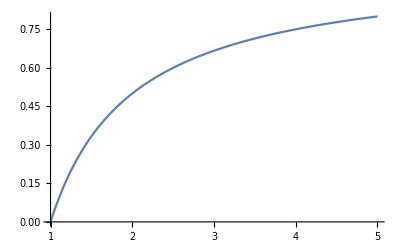

```mathematica
c0=1
Plot[(-c0+c1)/c1,{c1,1,5}]
```

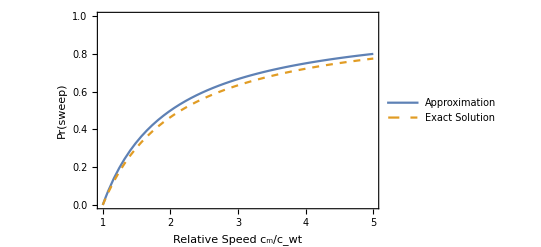

```mathematica
Plot[{(c-1)/c,gamma2[c]*(arci[c]+Log[delta[c]])},{c,1,5}, PlotStyle-> {Line, Dashed}, PlotRange->{0,1}, Frame-> True, FrameLabel->{Style["Relative Speed c_m/c_wt",Bold,12], Style["Pr(sweep)",Bold,12]}, RotateLabel->True, PlotLegends->Placed[{"Approximation","Exact Solution"},Center]]
```